```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"C:\\Users\\vfigu\\OneDrive\\Documentos\\Wolfram\\Teste1\\ScalarProxy"]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},Model->"C:\\Users\\vfigu\\OneDrive\\Documentos\\Wolfram\\Teste1\\ScalarProxy\\ScalarProxy", GenericModel ->"C:\\Users\\vfigu\\OneDrive\\Documentos\\Wolfram\\Teste1\\ScalarProxy\\ScalarProxy"];
```

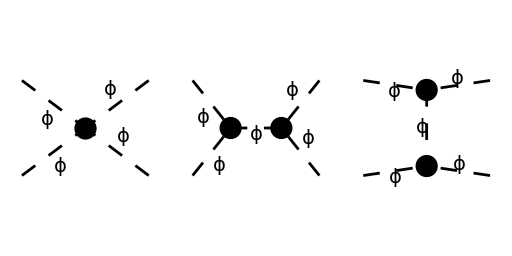

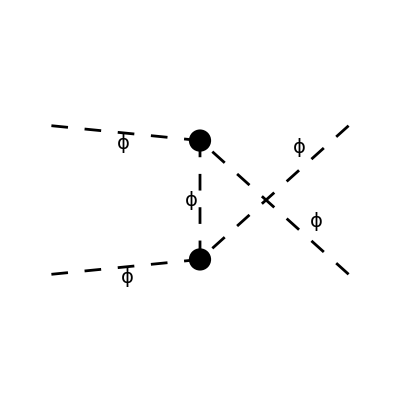

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{},ChangeDimension->4,List->False]
```

-3 ⅈ g^2+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[-k1-k2],Momentum[-k1-k2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[k1+k2],Momentum[k1+k2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k1-p2],Momentum[k1-p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k1+p2],Momentum[-k1+p2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k2-p2],Momentum[k2-p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k2+p2],Momentum[-k2+p2]])

```mathematica
kinRules={Pair[Momentum[p1],Momentum[p1]]->0,Pair[Momentum[p2],Momentum[p2]]->0,Pair[Momentum[k2],Momentum[k2]]->0,Pair[Momentum[k1],Momentum[k1]]->0};
```

```mathematica
amp[0]=amp[0] // Contract // SUNSimplify
```

-3 ⅈ g^2+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k1],Momentum[k1]]-ⅈ g Pair[Momentum[k2],Momentum[k2]]-ⅈ g Pair[Momentum[k1+k2],Momentum[k1+k2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k1-k2],Momentum[-k1-k2]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]-ⅈ g Pair[Momentum[p2],Momentum[p2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k1],Momentum[k1]]-ⅈ g Pair[Momentum[k1-p2],Momentum[k1-p2]]-ⅈ g Pair[Momentum[p2],Momentum[p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[k2],Momentum[k2]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]-ⅈ g Pair[Momentum[-k1+p2],Momentum[-k1+p2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k2],Momentum[k2]]-ⅈ g Pair[Momentum[k2-p2],Momentum[k2-p2]]-ⅈ g Pair[Momentum[p2],Momentum[p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[k1],Momentum[k1]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]-ⅈ g Pair[Momentum[-k2+p2],Momentum[-k2+p2]])

```mathematica
ampK = amp[0]/. kinRules
```

-3 ⅈ g^2+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[-k1-k2],Momentum[-k1-k2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[k1+k2],Momentum[k1+k2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k1-p2],Momentum[k1-p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k1+p2],Momentum[-k1+p2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k2-p2],Momentum[k2-p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k2+p2],Momentum[-k2+p2]])

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t, u, p1 , p2, k1 , k2 , 0 , 0 , 0 , 0 ];
```

```mathematica
amp[0]
```

-3 ⅈ g^2+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[-k1-k2],Momentum[-k1-k2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[k1+k2],Momentum[k1+k2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k1-p2],Momentum[k1-p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k1+p2],Momentum[-k1+p2]])+ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[k2-p2],m]] (ⅈ g m^2-ⅈ g Pair[Momentum[k2-p2],Momentum[k2-p2]]) (ⅈ g m^2-ⅈ g Pair[Momentum[-k2+p2],Momentum[-k2+p2]])

```mathematica
ampK1 = ampK // ExpandScalarProduct
```

-(ⅈ g^2 (6 s t u+m^2 (-t u+s (t+u))))/(s t u)

```mathematica
ampK =FeynAmpDenominatorExplicit[ampK] /. s->-t-u
```

-(ⅈ g^2 (6 t (-t-u) u+m^2 (-t u+(-t-u) (t+u))))/(t (-t-u) u)

```mathematica
ampK // FullSimplify
```

-(ⅈ g^2 (6 t u (t+u)+m^2 (t^2+3 t u+u^2)))/(t u (t+u))